# Explorations: String Manipulation

When working with text and strings, often your data will need some level of cleaning. If we want to look at common words in NKS, we can use WordCloud:

```mathematica
nks=ResourceData["Full Text of A New Kind of Science"];
```

```mathematica
WordCounts[nks]
```

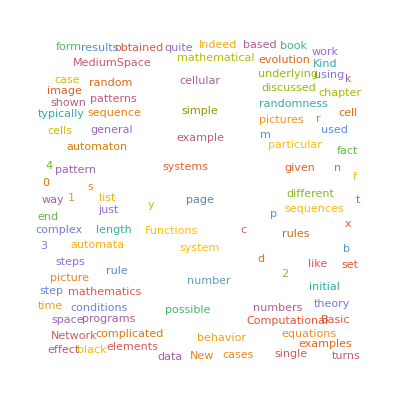

```mathematica
WordCloud[nks,IgnoreCase->True]
```

While WordCloud automatically removes stopwords (the, and, etc.), because of things like equations and variables we’re getting some noise in our WordCloud.

#### Activity #1

Clean up the data from NKS to remove non-words from our dataset.

#### Activity #2

Pick your own piece of plaintext from the Wolfram Data Repository and make a cleaned WordCloud for your text!

#### Activity #3

Some types of text can lend themselves to “easy” analysis based on key words or formatting. The play in MIT’s database of Shakespeare’s work are one such example. Let’s look at some of the features of Romeo and Juliet!

We’ll start with importing! We’re going to ignore the prologue, and we can import the full text as well as the text by individual scenes using the structure of the database we’re pull from.

```mathematica
rAndJFull=Import["http://shakespeare.mit.edu/romeo_juliet/romeo_juliet/full.html","HTML"];
```

We’ll need the scenes in a string format, i.e. Act 1 Scene 1 would be “1.1”. Acts 1, 3, and 4 each have five scenes. Act 2 has six scenes. Act 5 has three scenes.

```mathematica
sceneNumbers=DeleteCases[Flatten@Table[ToString[i]<>"."<>ToString[j],{i,1,5},{j,1,6}],"1.6"|"3.6"|"4.6"|"5.4"|"5.5"|"5.6"]
```

{1.1,1.2,1.3,1.4,1.5,2.1,2.2,2.3,2.4,2.5,2.6,3.1,3.2,3.3,3.4,3.5,4.1,4.2,4.3,4.4,4.5,5.1,5.2,5.3}

```mathematica
scenes=Import["http://shakespeare.mit.edu/romeo_juliet/romeo_juliet."<>#<>".html","Source"]&/@sceneNumbers;
```

Take a look at the formatting of the text to see what you can leverage to find the names of all the characters and split the text into lines. You may need to do some cleaning for formatting differences.

Hint:

Because we’re importing the HTML version of the script, every character name is going to have a wrapper to bold the name. If you’re having trouble with this, look up Shortest[]

Hint 2:

Use pattern matching to find the text that occurs between “<b>” and “</b>”

From here, complete one of the three following prompts (or all three) for Romeo and Juliet. If you have a different Shakespeare play you’d rather do, you can find the text on the same site, though more popular plays will likely have fewer formatting inconsistencies.

Look at how frequently certain words appear in the play and who says them. Come up with a visualization.

Create a graphic that visualizes when each character is speaking. For inspiration, you can look up the Wolfram|Alpha page for the play. As an extra, have the graphic also factor in the length of their line.

If you also do the first prompt, you could combine into one visual.

Create a social network of the characters in the play. Use either text distance or entrances/exits.